```mathematica
ClearAll["Global`*"];
```

```mathematica
dataStandingVariation=Import[NotebookDirectory[]<>"../Data/"<>"Table_standing_variants_seedbank_strength_1herb_10no.txt","CSV"];
```

```mathematica
data=Import[NotebookDirectory[]<>"../Data/"<>"Table_MGWP_SeedBankStrength.txt","CSV"];
```

## Rescue probability under varying strong seed banks

### Rescue probability for the MGWP with one two allelic locus in a diploid genome

#### Parameters of the model

```mathematica
b=0.9 140;
dZ=0.35;
gZ = 0.2;
f=0.9 13000;
dS=0.94;
c=0.3;
kc=0.5;
cr = {0,kc c,c};
```

```mathematica
T=b(1-dZ)gZ;
S = (1-cr)f(1-dS);
```

```mathematica
p=0.95;
dB=0.48 g /(1-g)(1-0.3)/0.3;
μ=10^-8;
hl=0.998;
ht=0.985;
kh=0.5;
densSeeds=80;
densPlants=1;
hL = {hl,(1-kh) hl, 0};
hT = {ht,(1-kh) ht, 0};
```

```mathematica
M={(1-μ)^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ(1-μ) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+μ^2{{0,0,0},{0,0.25,0.5},{0,0.5,1}},2 μ (1-μ) {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+((1-μ)^2 +μ^2) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+2 μ (1-μ){{0,0,0},{0,0.25,0.5},{0,0.5,1}},μ^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+{{0,0,0},{0,0.25,0.5},{0,0.5,1}}}//N;
```

#### Standing genetic variation

```mathematica
v=dataStandingVariation⟦2;;,All⟧;
```

#### Rescue probability

```mathematica
pRescue[A_,q_,i_]:=1- Exp[A  (v[[i,6]] (q[[1]]-1)+ v[[i,7]]  (q[[2]]-1)+v[[i,8]](q[[3]]-1)+v[[i,3]]  (q[[4]]-1)+ v[[i,4]]  (q[[5]]-1)+v[[i,5]] (q[[6]]-1))]//Quiet;
```

#### Parameters of the offspring distributions

```mathematica
λ[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))g (1-hL[[j]])+KroneckerDelta[j,i]T(1-hT[[j]]);
λm[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))(1-g);
```

```mathematica
α[g_,i_]:=(1-0.48 g /(1-g)(1-0.3)/0.3) g (1-hL[[i]]);
β[g_]:=(1-0.48 g /(1-g)(1-0.3)/0.3) (1-g);
γ[g_,i_]:=(0.48 g /(1-g)(1-0.3)/0.3+(1-0.48 g /(1-g)(1-0.3)/0.3) g hL[[i]]);
```

#### Parameters of the reduced set of equations for the extinction probabilities

```mathematica
Λ[i_,j_]:=λ[i,j]+λm[i,j]α[g,j]/(1-β[g]);
Γ[i_]:=Exp[Sum[λm[i,j](γ[g,j]/(1-β[g])-1)-λ[i,j],{j,1,3}]];
```

#### Extinction probabilities

```mathematica
q={q1,q2,q3}/.Table[FindRoot[{q1==Γ[1]Exp[Λ[1,1] q1+Λ[1,2] q2+Λ[1,3] q3],q2==Γ[2]Exp[Λ[2,1] q1+Λ[2,2] q2+Λ[2,3] q3],q3==Γ[3]Exp[Λ[3,1] q1+Λ[3,2] q2+Λ[3,3] q3]},{{q1,0},{q2,0},{q3,0}}]//Quiet,{g,0.01,0.47,0.001}];
```

```mathematica
q=MapThread[{#1[[1]],#1[[2]],#1[[3]],(α[#2,1]#1[[1]]+γ[#2,1])/(1-β[#2]),(α[#2,2]#1[[2]]+γ[#2,2])/(1-β[#2]),(α[#2,3]#1[[3]]+γ[#2,3])/(1-β[#2])}&,{q,Range[0.01,0.47,0.001]}];
```

#### Rescue probability as a function of germination probability (adapted seed bank mortality)

```mathematica
pR=MapThread[pRescue[10^2,#1,#2]&,{q,Range[1,Length[v[[All,1]]]]}];
```

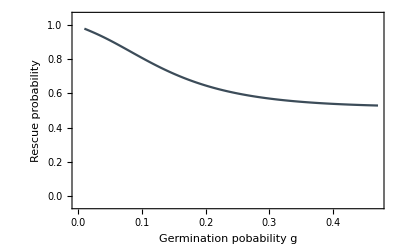

```mathematica
SeedBankPlot=ListPlot[Partition[Riffle[Table[g,{g,0.01,0.47,0.001}],pR],2],PlotRange->{Automatic,{-.05,1.05}},Joined->True,Mesh->False,MeshStyle->PointSize[0.018],PlotStyle->Directive[Full,RGBColor["#3C4C59"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Germination pobability g","Rescue probability"},Axes->False,PlotRange->{{-0.001,0.501},{-0.01,1.01}}]
```

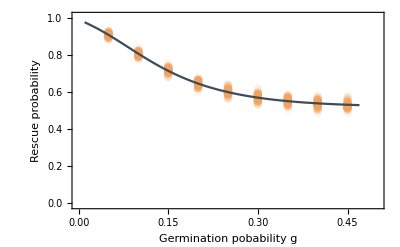

```mathematica
Show[ListPlot[data⟦2;;,{1,4}⟧,PlotStyle->Directive[RGBColor["#F2A35E"],PointSize[0.015],Opacity[0.1]]],SeedBankPlot,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Germination pobability g","Rescue probability"},Axes->False,PlotRange->{{-0.001,0.501},{-0.01,1.01}}]
```